Курсов проект по “Компютърни числени методи”

Изготвил: Емил Григоров Медаров
																		ФН: 2001262013

# Задача 4. Дадена е функцията f(x)=ln(x^2+Px+Q)+ (Px^3+Q)/(√x+P). Табулирайте f(x) в точките {2,2.3,2.7,2.9,3.2,3.6,4.1}. По получената таблица интерполирайте с линеен или квадратичен сплайн и намерете приближена стойност в точката 𝑥=3 и 𝑥=3.9. Оценете грешката.

```mathematica
(*Тази команда чисти всички променливи,за да започнем с чисто състояние.*)
Clear[x,y,n,a,b,g,t,z] 


(*Тук се дефинира функцията f(x,P,Q),която представлява нашата функция.Тя зависи от параметрите P и Q.*)
f[x_,P_,Q_]:=Log[x^2+P x+Q]+(P x^3+Q)/Sqrt[x+P]


(*Задавам стойностите на P и Q*)
P=3.3; 
Q=4.5;


(*Тук се дефинират точките x и изчисляват съответните стойности на функцията y.*)
x={2,2.3,2.7,2.9,3.2,3.6,4.1}; 
y=f[x,P, Q];

(*Пресмята броя на интервалите в таблицата на точките.*)
n=Length[x]-1;

(*Този ред създава графика на точките (x,y) в червено.*)
g1=ListPlot[Table[{x[[i]],y[[i]]},{i,1,n+1}],PlotStyle->Red];

(*Инициализират се променливите a,b и g със стойности на y.*)
a=b=y;
g=y;

(*Изчисляват се кофициентите b за интерполация.*)
For[i=1,i<=n,i++,b[[i]]=(y[[i+1]]-y[[i]])/(x[[i+1]]-x[[i]])];


(*Дефинират се точките z1 и z2,след което се изчисляват интерполациите в тези точки.*)
z1=3;
z2=3.9;
yy1=a[[1]]+b[[1]]*(z1-x[[1]]);
yy2=a[[1]]+b[[1]]*(z2-x[[1]]);


(*Извежда текст на конзолата.*)
Print["Таблицата с линейните сплайни е:"]


(*Този блок цикли из всички интервали и изчислява линейни сплайнове за всеки интервал,след което ги визуализира и извежда информация за тях.*)
For[k=1,k<=n,k++,f[t_]:=a[[k]]+b[[k]]*(t-x[[k]]);
g[[k]]=Plot[f[t],{t,x[[k]],x[[k+1]]},AxesOrigin->{0,0}];
Print["    интервал: [",x_⟦k⟧,";",x_⟦k+1⟧,"]   f[",k,"] = ",f[t]]
];


(*Извеждат се стойностите на сплайновете в точките z1 и z2.*)
Print["Стойността на сплайна в търсената точка z1 = ",z1," e ",yy1];
Print["Стойността на сплайна в търсената точка z2 = ",z2," e ",yy2];
```

Таблицата с линейните сплайни е:

интервал: [2;2.3]   f[1] = 16.1368+18.6235 (-2+t)

интервал: [2.3;2.7]   f[2] = 21.7239+24.1518 (-2.3+t)

интервал: [2.7;2.9]   f[3] = 31.3846+29.2917 (-2.7+t)

интервал: [2.9;3.2]   f[4] = 37.2429+33.8892 (-2.9+t)

интервал: [3.2;3.6]   f[5] = 47.4097+40.7395 (-3.2+t)

интервал: [3.6;4.1]   f[6] = 63.7055+50.2158 (-3.6+t)

Стойността на сплайна в търсената точка z1 = 3 e 34.7603

Стойността на сплайна в търсената точка z2 = 3.9 e 51.5215

Интерполация в точка x=3: 34.7603, Истинска стойност: 40.4439, Грешка: 5.68355

Интерполация в точка x=3.9: 51.5215, Истинска стойност: 78.1135, Грешка: 26.592

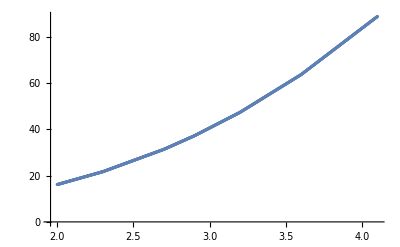

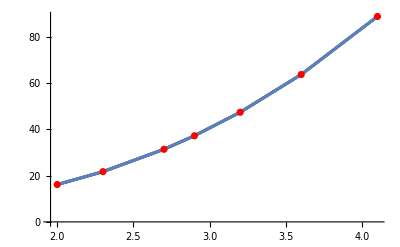

```mathematica
(*trueValue1 и trueValue2 съхраняват реалните стойности на функцията f в точките z1 и z2,използвайки зададените стойности на P и Q.*)
trueValue1=f[z1,P,Q];
trueValue2=f[z2,P,Q];


(*error1 и error2 изчисляват грешката между интерполираните стойности yy1 и yy2 и реалните стойности на функцията trueValue1 и trueValue2 с помощта на функцията Abs,която връща абсолютната стойност (положителната стойност) на разликата между две стойности.*)
error1=Abs[yy1-trueValue1];
error2=Abs[yy2-trueValue2];


(*Най-накрая информацията за интерполациите и грешките се извежда в конзолата с помощта на Print.Текстът,който се извежда,съдържа интерполираните стойности,реалните стойности и грешката за всяка точка.*)
Print["Интерполация в точка x=3: ",yy1,", Истинска стойност: ",trueValue1,", Грешка: ",error1];
Print["Интерполация в точка x=3.9: ",yy2,", Истинска стойност: ",trueValue2,", Грешка: ",error2];

(* графика на сплайна *)
np=1000;hh=(x_⟦n+1⟧-x_⟦1⟧)/np;
p={{x_⟦1⟧,y_⟦1⟧}};
For[i=1,i≤np,i++,xx=x_⟦1⟧+i*hh;
For[k=1,k≤n,k++,If[x_⟦k⟧≤xx && xx≤x_⟦k+1⟧,yy=a[[k]]+b[[k]]*(xx-x[[k]])];];
AppendTo[p,{xx,yy}];
];
g2=ListPlot[p]
(*Показване на графиката на линейния сплайн*)
Show[g2,g1]
```